# Interpolation

## Exempel från föreläsningen

## Exempel 1

Remove::rmnsm: There are no symbols matching "Global`*".

Koefficienter: {c[0]→2,c[1]→-1,c[2]→3}

p[x] = c[0]+(-1+x) c[1]+(-2+x) (-1+x) c[2] = 9-10 x+3 x^2

Med Mathematicas funktion Fit: p(x) = 9.-10. x+3. x^2

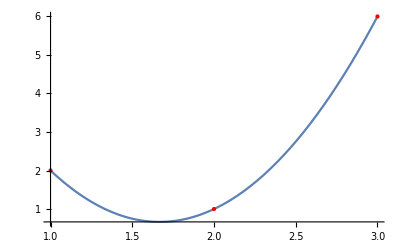

```mathematica
Remove["Global`*"]
xv={1,2,3};
fv={2,1,6};
n=Length[xv];
data=Transpose[{xv,fv}];
deg=n-1; (* p(x) av grad deg *)
p=c[0];
For[i=1,i<=deg,++i,
p+=Product[(x-xv[[k]]),{k,1,i}]*c[i];
]
const=Table[c[i],{i,0,deg}];
sol=Solve[Table[(p/.x->xv[[i]])==fv[[i]],{i,1,deg+1}],const];
Print["Koefficienter: ",sol[[1]]]
Print["p[x] = ",p," = " , Simplify[p/.sol[[1]]]]
pl=Plot[p/.sol[[1]],{x,xv[[1]],xv[[n]]}];
lp=ListPlot[data,PlotStyle->{Red,PointSize[Large]}];
Print["Med Mathematicas funktion Fit: p(x) = ", Fit[data,{1,x,x^2},x]]
Show[{pl,lp}]
```

## Exempel 2

1.0033-0.1715 x

1.0033-0.27331 x+0.254524 x^2

1.0033-0.267601 x+0.232098 x^2+0.0203869 x^3

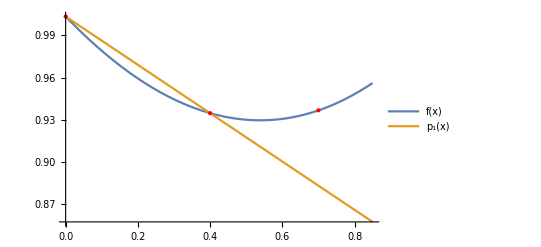

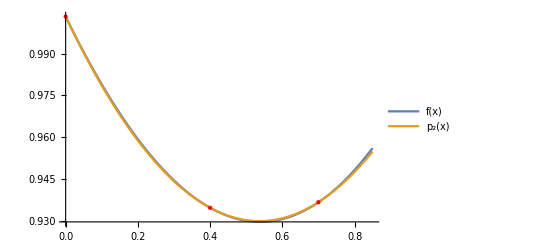

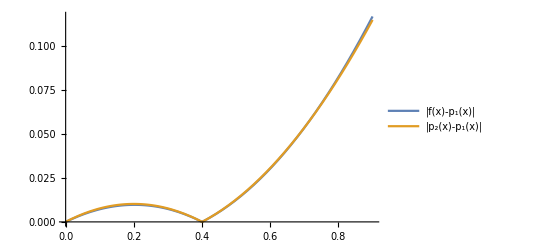

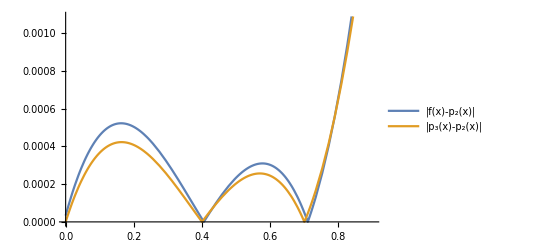

```mathematica
Remove["Global`*"]
f[x_]:=Exp[-x/5]*Cos[x/2]+ (x-0.1)^2/3
xv={0.0,0.4,0.7};
yv={1.0033,0.9347,0.9367};
epoint={0.8,0.9482};
data=Transpose[{xv,yv}];
lp1=ListPlot[data,PlotStyle->{Red,PointSize[Large]}];
p1=Fit[{data[[1]],data[[2]]},{1,x},x]
p2=Fit[data,{1,x,x^2},x]
lp2=ListPlot[data,PlotStyle->{{Red,PointSize[Large]}}];
data=Insert[data,epoint,4];
p3=Fit[data,{1,x,x^2,x^3},x]
plot1=Plot[{f[x],p1},{x,0,0.85},PlotLegends->{"f(x)","p_1(x)"}];
Show[{plot1,lp1}]
plot2=Plot[{f[x],p2},{x,0,0.85},PlotLegends->{"f(x)","p_2(x)"}];
Show[{plot2,lp2}]
Plot[{Abs[f[x]-p1],Abs[p2-p1]},{x,0,0.9},PlotLegends->{"|f(x)-p_1(x)|","|p_2(x)-p_1(x)|"}]
Plot[{Abs[f[x]-p2],Abs[p3-p2]},{x,0,0.9},PlotLegends->{"|f(x)-p_2(x)|","|p_3(x)-p_2(x)|"}]
```

### Exempel 4

Koefficienter: {c[0]→1,c[1]→2,d[0]→3,d[1]→-1}

s1[x] = c[0]+x c[1] = 1+2 x

s2[x] = d[0]+(-1+x) d[1] = 4-x

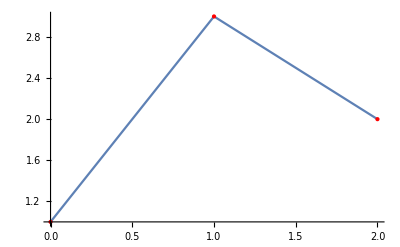

```mathematica
Remove["Global`*"]
xv={0,1,2};
fv={1,3,2};
n=Length[xv];
data=Transpose[{xv,fv}];
deg=1; (* s(x) spline-funktion av grad deg *)
s1[x_]=Sum[c[i](x-xv[[n-2]])^i,{i,0,deg}];
s2[x_]=Sum[d[i](x-xv[[n-1]])^i,{i,0,deg}];
const=Join[Table[c[i],{i,0,deg}],Table[d[i],{i,0,deg}]];
sol=Solve[{
s1[xv[[1]]]==fv[[1]],
s1[xv[[2]]]==s2[xv[[2]]]==fv[[2]],
s2[xv[[3]]]==fv[[3]]
},const
];
Print["Koefficienter: ",sol[[1]]]
Print["s1[x] = ",s1[x] ," = " , Simplify[s1[x]/.sol[[1]]]]
Print["s2[x] = ",s2[x]," = " ,Simplify[s2[x]/.sol[[1]]]]
s[x_]=Piecewise[{{s1[x],xv[[n-2]]<x<xv[[n-1]]},{s2[x],xv[[n-1]]<x<xv[[n]]}}];
pl=Plot[s[x]/.sol[[1]],{x,xv[[1]],xv[[n]]}];
lp=ListPlot[data,PlotStyle->{Red,PointSize[Large]}];
Show[{pl,lp}]
```

### Exempel 4 med hattfunktioner

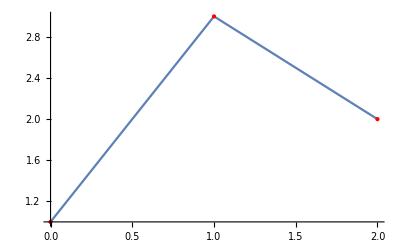

```mathematica
Remove["Global`*"]
xv={0,1,2};
fv={1,3,2};
n=Length[xv]-1;
phi={};
(*Första är "halvhatt"*)
AppendTo[phi,Piecewise[{{(xv[[2]]-x)/(xv[[2]]-xv[[1]]),xv[[1]]<x<xv[[2]]}}]];
For[i=2,i<=n,++i,
AppendTo[phi,Piecewise[
{{(x-xv[[i-1]])/(xv[[i]]-xv[[i-1]]),xv[[i-1]]<x<xv[[i]]},
{(xv[[i+1]]-x)/(xv[[i+1]]-xv[[i]]),xv[[i]]<x<xv[[i+1]]}}
]]
]
(*Sista är "halvhatt"*)
AppendTo[phi,Piecewise[{{(x-xv[[n]])/(xv[[n+1]]-xv[[n]]),xv[[n]]<x<xv[[n+1]]}}]];
s=fv.phi;
pl=Plot[s,{x,xv[[1]],xv[[n+1]]}];
data=Transpose[{xv,fv}];
lp=ListPlot[data,PlotStyle->{Red,PointSize[Large]}];
Show[pl,lp]
```

### Exempel 5

Koefficienter: {c[0]→1,c[1]→1,c[2]→13/4,c[3]→-9/4,d[0]→3,d[1]→3/4,d[2]→-7/2,d[3]→7/4}

s1[x] = c[0]+x c[1]+x^2 c[2]+x^3 c[3] = 1+x+(13 x^2)/4-(9 x^3)/4

s2[x] = d[0]+(-1+x) d[1]+(-1+x)^2 d[2]+(-1+x)^3 d[3] = -3+13 x-(35 x^2)/4+(7 x^3)/4

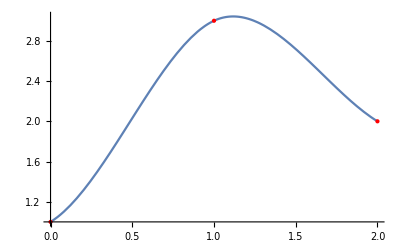

```mathematica
Remove["Global`*"]
xv={0,1,2};
fv={1,3,2};
{dfl,dfr}={1,-1};
n=Length[xv];
data=Transpose[{xv,fv}];
deg=3; (* s(x) spline-funktion av grad deg *)
s1[x_]=Sum[c[i](x-xv[[n-2]])^i,{i,0,deg}];
s2[x_]=Sum[d[i](x-xv[[n-1]])^i,{i,0,deg}];
const=Join[Table[c[i],{i,0,deg}],Table[d[i],{i,0,deg}]];
sol=Solve[{
s1[xv[[1]]]==fv[[1]],
s1[xv[[2]]]==s2[xv[[2]]]==fv[[2]],
s2[xv[[3]]]==fv[[3]],
s1'[xv[[2]]]==s2'[xv[[2]]],
s1''[xv[[2]]]==s2''[xv[[2]]],
s1'[xv[[1]]]==dfl,
s2'[xv[[3]]]==dfr
},const
];
Print["Koefficienter: ",sol[[1]]]
Print["s1[x] = ",s1[x] ," = " , Simplify[s1[x]/.sol[[1]]]]
Print["s2[x] = ",s2[x]," = " ,Simplify[s2[x]/.sol[[1]]]]
s[x_]=Piecewise[{{s1[x],xv[[n-2]]<x<xv[[n-1]]},{s2[x],xv[[n-1]]<x<xv[[n]]}}];
pl=Plot[s[x]/.sol[[1]],{x,xv[[1]],xv[[n]]}];
lp=ListPlot[data,PlotStyle->{Red,PointSize[Large]}];
Show[{pl,lp}]
```